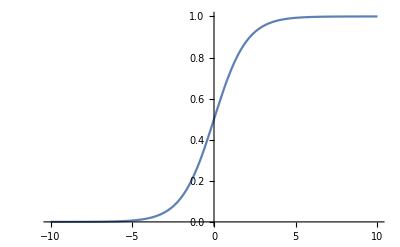

```mathematica
fsigmoid[x_]:=1/(Exp[-x]+1);(*シグモイド関数*)
(*test*)
Plot[fsigmoid[x],{x,-10,10}]
```

```mathematica
(*fout: 前の層の出力vxから次の層の出力を計算する関数。mWはリンクの重み行列(行列なので先頭にmをつけた)*)
```

```mathematica
fout[mW_List,vx_List]:=Module[{vu,vy},
vu=mW.vx;(*リンクの重みmWと前層の出力の行列積で各unitに入る活性ベクトルを計算*)
vy=Map[fsigmoid,vu];(*vuの各成分をsigmoid関数に入れて出力計算*)
Return[vy];
];
```

```mathematica
fout[{{w11,w12},{w21,w22}},{x1,x2}]
```

{1/(1+ⅇ^(-w11 x1-w12 x2)),1/(1+ⅇ^(-w21 x1-w22 x2))}

```mathematica
fforward[vx_]:=Module[{},(*作業用変数はないので作業用変数のリストは空リスト*)
gvy1=fout[gW1,vx];(*隠れ層(第1unit層)の出力計算*)
gvy2=fout[gW2,gvy1];(*出力層(第2unit層)の出力計算*)
Return[gvy2];(*出力層の出力がNNとしての出力*)
];
```

```mathematica
(*記号計算を使ったtest。入力unit2つ。隠れ層unit3つ、出力unit2つの場合*)
gW1={{a11,a12},{a21,a22}};
gW2={{b11,b12},{b21,b22}};
fforward[{x1,x2}](*NNとしての出力(=出力層の出力)*)
```

{1/(1+ⅇ^(-b11/(1+ⅇ^(-a11 x1-a12 x2))-b12/(1+ⅇ^(-a21 x1-a22 x2)))),1/(1+ⅇ^(-b21/(1+ⅇ^(-a11 x1-a12 x2))-b22/(1+ⅇ^(-a21 x1-a22 x2))))}

```mathematica
gvy1(*隠れ層の出力。fforwardでセットされた値を確かめる。*)
```

{1/(1+ⅇ^(-a11 x1-a12 x2)),1/(1+ⅇ^(-a21 x1-a22 x2))}

```mathematica
fbackward[vx_List,vy1_List,vy2_List,vt_List,eta_]:=Module[{vs2,vs1,mp2,mp1},
vs2=(vy2-vt)*(vy2*(1-vy2));(*誤差(vy2-vt)の「unit層2逆伝播」*)
vs1=(vs2.gW2)*vy1*(1-vy1);(*「link層2とunit層1を逆伝播」。vy1には直前の前方計算で得たgvy1の値を入れること*)
gW2=gW2-eta*Outer[Times,vs2,vy1];(*gW2の調整*)
gW1=gW1=eta*Outer[Times,vs1,vx];(*gW1の調整*)
(*結果はグローバル変数gW1,gW2に残るので、返値はなし*)
];
```

```mathematica
(*記号計算を使った簡単なtest*)
Clear[c1,c2];gW1={{a11,a12},{a21,a22}};
gW2={{b11,b12},{b21,b22}};
vx={a1,a2};gvy2={c1,c2};gvy1={b1,b2};gvt={d1,d2};
fbackward[vx,gvy1,gvy2,gvt,eta];
Print[MatrixForm[gW2]];
  Print[MatrixForm[gW1]];(*結果はグローバル変数gW32,gW21に残る*)
```

(b11-b1 (1-c1) c1 (c1-d1) eta | b12-b2 (1-c1) c1 (c1-d1) eta
b21-b1 (1-c2) c2 (c2-d2) eta | b22-b2 (1-c2) c2 (c2-d2) eta)

(a1 (1-b1) b1 (b11 (1-c1) c1 (c1-d1)+b21 (1-c2) c2 (c2-d2)) eta | a2 (1-b1) b1 (b11 (1-c1) c1 (c1-d1)+b21 (1-c2) c2 (c2-d2)) eta
a1 (1-b2) b2 (b12 (1-c1) c1 (c1-d1)+b22 (1-c2) c2 (c2-d2)) eta | a2 (1-b2) b2 (b12 (1-c1) c1 (c1-d1)+b22 (1-c2) c2 (c2-d2)) eta)

```mathematica
gvx={0,1};gvt={1,1,0};(*入力gvx=(0,1)、正答をgvt={1,1,0}とする*)
```

```mathematica
(*重みを入れる行列の初期値を用意する。まず各層のUnit数を設定。*)
gn0=Length[gvx];(*入力層のUnit数。入力の成分数と同じ*)
gn2=Length[gvt];(*出力層のUnit数。出力の成分数と同じ*)
gn1=3;(*隠れ層のUnit数。これは制限ないので、試行錯誤で適当な値を探す*)

SeedRandom[1234];(*乱数のシードを決めておく*)
(*Unitの間の結合重み行列。初期値は-0.1~0.1の間でランダムに選んでおく*)
gW1=RandomReal[{-0.1,0.1},{gn1,gn0}];(*第1link層の重み: gn1xgn0 の行列*)
gW2=RandomReal[{-0.1,0.1},{gn2,gn1}];(*第2link層の重み: gn2xgn1 の行列*)
Print[MatrixForm[gW1],MatrixForm[gW2]](*確認のため表示*)
```

(0.0753217 | 0.00439285
-0.0827553 | -0.0244174
-0.0976711 | 0.0854532)(0.00875135 | -0.00413367 | -0.0509302
0.0519792 | 0.0969986 | -0.056591
-0.00819656 | 0.0769458 | 0.0167709)

```mathematica
vy=fforward[gvx](*前方計算で現パラメータでの出力を計算，vyに入れる*)
```

{0.493948,0.511111,0.510658}

```mathematica
eta=5.0;fbackward[gvx,gvy1,vy,gvt,eta];
(*誤差逆伝播 fbackwardでgW2,gW1を調整．学習率etaは5.0にしてみる*)
```

```mathematica
vy=fforward[gvx](*調査後のgW1,gW2で再び前方計算．前の結果より正答{1,1,0}に近づいているはず*)
```

{0.612232,0.62467,0.391378}

```mathematica
(*繰り返し実行し，誤差の大きさがどうなるか見てみる*)
gosalist={};(*誤差の時系列を入れておくためのリスト*)
For[i=0,i≤10,i=i+1,
vy=fforward[gvx];
gosalist=Append[gosalist,(1/2)*(vy-gvt).(vy-gvt)];
fbackward[gvx,gvy1,vy,gvt,eta];
];
```

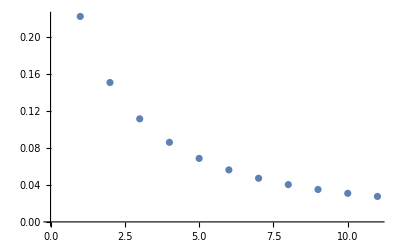

```mathematica
ListPlot[gosalist]
```

```mathematica
gInpList={{0,0},{0,1},{1,0},{1,1}};
gKyousiList={{0,0},{0,1},{0,1},{1,1}};
gn0=Length[gInpList[[1]]];(*gn0は入力の1つ1つが持つ成分の個数なので，gInpListの最初の入力の成分個数で決まる*)
gn2=Length[gKyousiList[[1]]];(*gn2は出力の成分の個数=教師信号の成分の個数*)
gn1=3;(*隠れ層の個数は制限がなく，自分で選ぶ自由度がある．ここでは3個に選ぶ*)
```

```mathematica
(*unit間の結合の重み．初期とは-0.1~0.1の間でランダムに選んでおく*)
SeedRandom[1234];
gW1=RandomReal[{-0.1,0.1},{gn1,gn0}];(*gn1xgn0の行列*)
gW2=RandomReal[{-0.1,0.1},{gn2,gn1}];(*gn2xgn1の行列*)
Print[MatrixForm[gW1],MatrixForm[gW2]];
```

(0.0753217 | 0.00439285
-0.0827553 | -0.0244174
-0.0976711 | 0.0854532)(0.00875135 | -0.00413367 | -0.0509302
0.0519792 | 0.0969986 | -0.056591)

```mathematica
flearnrepeat[eta_,kurikaesiSuu_]:=Module[
{ii,k,vx,vy,vs2,vs1,vt,errtbl},(*作業用変数のリスト*)
errtbl=Table[{},{k,1,Length[gKyousiList]}];(*正答ごとの誤差を入れるリストを用意*)
For[ii=1,ii≤kurikaesiSuu,ii++,(*調整を繰り返す．学習の主要部分*)
k=RandomInteger[{1,Length[gKyousiList]}];(*入力ー正答ペアの番号kをランダムに取る*)
vx=gInpList[[k]];vt=gKyousiList[[k]];(*k番目の入力と教師信号を取り出す．*)
vy=fforward[vx];(*その入力で順伝播計算．gvy1も更新*)

errtbl[[k]]=Append[errtbl[[k]],0.5*(vy-vt).(vy-vt)];(*出力と正答間の誤差を入れる*)
fbackward[vx,gvy1,vy,vt,eta];(*誤差逆伝播で重みgW2,gW1を調整*)
];(*以上をkurikaesiSuuだけ繰り返す*)

gerrtbl=errtbl;(*誤差のリストをグローバル変数gerrtblに残しておく*)
vyList=Table[fforward[vx],{vx,gInpList}];(*学習後の重みで計算*)
Return[vylist];(*その結果を返り値とする*)
];
```